```mathematica
shape=GeoGraphics[{EdgeForm[Black],FaceForm[Red],Polygon[Entity["Country","Iran"]]},GeoBackground->None,PlotRange->All];
```

```mathematica
centre=Binarize[shape]//ImageMesh//RegionCentroid
```

{224.414,177.395}

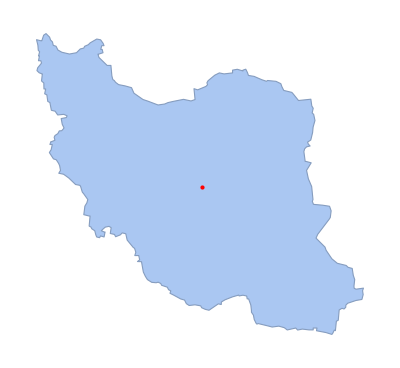

```mathematica
Show[Binarize[shape]//ImageMesh,Graphics[{Red,PointSize[Large],Point[centre]}]]
```

```mathematica
CountryData["Iran","CenterLocationLink"]
```

http://maps.google.com/maps?q=+32,+53&z=5&t=h

```mathematica
"q"/.URLParse[First@CountryData["Iran","CenterLocationLink"]]["Query"]//Interpreter["GeoCoordinates"]
```

GeoPosition[{32,53}]

```mathematica
loc1=Entity["Country","Iran"][EntityProperty["Country","Position"]]
```

GeoPosition[{32.,53.}]

```mathematica
centre=Entity["Country","Iran"]["Polygon"]//DiscretizeGraphics//RegionCentroid//Reverse//GeoPosition
```

GeoPosition[{32.5686,54.3011}]

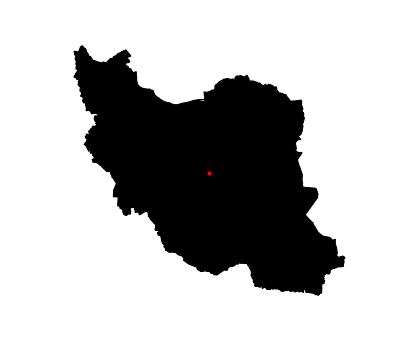

```mathematica
GeoGraphics[{EdgeForm[Black],FaceForm[Black],Polygon[Entity["Country","Iran"]],Red,PointSize@Large,Point@centre},GeoBackground->None,PlotRange->All]
```

```mathematica
countryRegion3D[meshI:(_MeshRegion|_BoundaryMeshRegion)]:=Block[{mesh=Quiet@TriangulateMesh@DiscretizeRegion@meshI},If[Head[mesh]=!=MeshRegion,Missing[],MeshRegion[GeoPositionXYZ[GeoPosition[Reverse/@MeshCoordinates[mesh]]][[1]],MeshCells[mesh,2]]]]
```

```mathematica
r=DiscretizeGraphics[Polygon/@Map[Reverse,Entity["Country","Iran"]["Polygon"][[1,1]],{2}]];
```

```mathematica
countryRegion3D[r]
```

-Graphics3D-

```mathematica
GeoPosition@GeoPositionXYZ@RegionCentroid@countryRegion3D@r
```

GeoPosition[{32.5247,54.4659,-25908.}]